# Aproximações

### Formulação variacional : a u'' + b u' + c u = f (x)

Convectivo dominante que oscila : a = -1, b = 100000, c = 0
Convectivo dominante que funciona para p=1, nel = 10: a=-1, b=100, c=0

### Dados de Entrada:

(-1+x) x^2

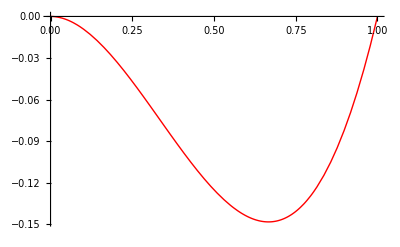

```mathematica
a=-1;
b=0; 
c=0;
Uexata=x^2 (x-1)(*E^(20 x) (x-1)*)
DUexata=D[Uexata,x];
Exat=Plot[Uexata,{x,0,1},PlotStyle->{Red},PlotRange->All]
DExat=Plot[DUexata,{x,0,1},PlotStyle->{Red},PlotRange->All];
f=a D[Uexata,{x,2}]+b D[Uexata,x]+c Uexata;
```

## por Elementos Finitos - Linear (Referências Globais)

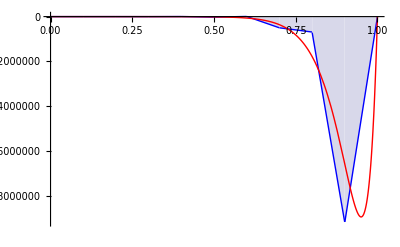

```mathematica
Nelem=10;
ElFinLinG[n_,a_,b_,c_,var_,f_]:=Block[{h,α,K,F,Un,DUn},
h=1./n;
Fi=Table[Piecewise[{{(var-(i-1)*h)/h,var≥(i-1)*h&&var≤i*h},{((i+1)*h-var)/h,var≥i*h&&var≤(i+1)*h},{0,var<(i-1)*h&&var>(i+1)*h}}],{i,1,n-1}];
Fil=Table[D[Fi[[i]],var],{i,1,n-1}];
K=Table[0,{n-1},{n-1}];
For[i=1,i<n,i++,For[j=1,j<n,j++,K[[i,j]]=Integrate[-a*Fil[[i]]*Fil[[j]]+b*Fil[[j]]*Fi[[i]]+c*Fi[[i]]*Fi[[j]],{var,0,1}]  ]];
F=Table[∫_0^1 f*Fi[[i]]ⅆvar,{i,1,n-1}];
α=LinearSolve[N[K],N[F]];
Un=α.Fi;
DUn=D[Un,x];

Plot[Un,{var,0,1},PlotStyle->{Blue},Filling->Axis,PlotRange->All]
(*Plot[DUn,{var,0,1},PlotStyle->{Blue},Filling->Axis,PlotRange->All]*)
]
ElFin=ElFinLinG[Nelem,a,b,c,x,f];
Show[ElFin,Exat]
```

## por Elementos Finitos - Quadrático (Referências Globais)

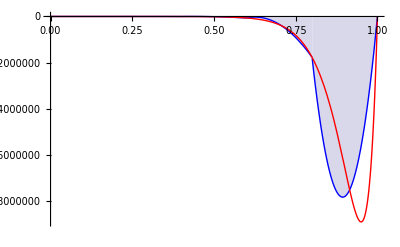

```mathematica
Nelem=5;
ElFinQuadG[n_,a_,b_,c_,var_,f_]:=Block[{h,α,K,F,Un},
h=1./(2*n);
Fi=Table[If[OddQ[i]==True,Piecewise[{{1-i^2+(2 i var)/h-var^2/h^2,var≥(i-1)*h&&var≤(i+1)*h},{0,var<(i-1)*h&&var>(i+1)*h}}],Piecewise[{{((h (-2+i)-var) (h (-1+i)-var))/(2 h^2),var≥(i-2)*h&&var≤i*h},{((h+h i-var) (h (2+i)-var))/(2 h^2),var≥i*h&&var≤(i+2)*h},{0,var<(i-2)*h&&var>(i+2)*h}}]],{i,1,2*n-1}];
Fil=Table[D[Fi[[i]],var],{i,1,2*n-1}];
K=Table[0,{2*n-1},{2*n-1}];
For[i=1,i<2*n,i++,For[j=1,j<2*n,j++,K[[i,j]]=∫_0^1 (-a*Fil[[i]]*Fil[[j]]+b*Fil[[j]]*Fi[[i]]+c*Fi[[i]]*Fi[[j]])ⅆvar  ]];
F=Table[∫_0^1 f*Fi[[i]]ⅆvar,{i,1,2*n-1}];
α=LinearSolve[N[K],N[F]];
Un=α.Fi;
DUn=D[Un,x];

Plot[Un,{var,0,1},PlotStyle->{Blue},Filling->Axis,PlotRange->All]
(*Plot[DUn,{var,0,1},PlotStyle->{Blue},Filling->Axis,PlotRange->All]*)
]
ElFin=ElFinQuadG[Nelem,a,b,c,x,f];
Show[ElFin,Exat]
```

## Método dos Elementos Finitos

{0.,-2.505,-0.0320016,-2.561,-0.0960024,-2.625,-0.144002,-2.649,-0.128002,-2.585,0.}

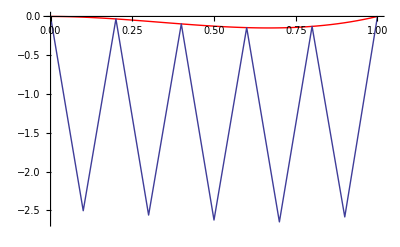

```mathematica
nel=10;
nnodes=nel+1;
L=1;
DEBUG=0;

phi[xil_,xfl_]={-(x-xfl)/(xfl-xil),(x-xil)/(xfl-xil)};
If[DEBUG==1,Plot[{phi[-2,-1.2][[1]],phi[-2,-1.2][[2]]},{x,-2,-1.2},PlotRange->All]]
dphi[xil_,xfl_]={D[phi[xil,xfl][[1]],x],D[phi[xil,xfl][[2]],x]};
If[DEBUG==1,Plot[{dphi[-1,1][[1]],dphi[-1,1][[2]]},{x,-1,1}]]


K=Table[0,{nnodes},{nnodes}];
F=Table[0,{nnodes}];
For[iel=1,iel≤nel,iel++,
xi=(iel-1)*(L/nel);
xf=xi+(L/nel);
KLocal=Table[ Integrate[ -a dphi[xi,xf][[i]] dphi[xi,xf][[j]]+b phi[xi,xf][[i]] dphi[xi,xf][[j]]+c phi[xi,xf][[i]] phi[xi,xf][[j]],{x,xi,xf}], {i,1,2},{j,1,2}];
If[DEBUG==1,
Print[MatrixForm[KLocal]];
]
For[i=0,i≤1,i++,
For[j=0,j≤1,j++,
K[[iel+i,iel+j]]+=KLocal[[i+1,j+1]];
];
F[[iel+i]]+=Integrate[f phi[xi,xf][[i+1]],{x,xi,xf}];
];
];

If[DEBUG==1,
Print[MatrixForm[K]];
Print[MatrixForm[F]];
]

(** Condicoes de contorno *)
xi=0;
xf=L/nel;
KLocal=Table[ Integrate[ -a dphi[xi,xf][[i]] dphi[xi,xf][[j]]+b phi[xi,xf][[i]] dphi[xi,xf][[j]]+c phi[xi,xf][[i]] phi[xi,xf][[j]],{x,xi,xf}], {i,1,2},{j,1,2}];
For[j=1,j≤nnodes,j++,
K[[1,j]]=0;
]
K[[1,1]]=1;
F[[1]]=Uexata/.x->0; (**Condicao Dirichlet igual a zero em x=0 *)
xi=L-L/nel;
xf=L;
KLocal=Table[ Integrate[ -a dphi[xi,xf][[i]] dphi[xi,xf][[j]]+b phi[xi,xf][[i]] dphi[xi,xf][[j]]+c phi[xi,xf][[i]] phi[xi,xf][[j]],{x,xi,xf}], {i,1,2},{j,1,2}];
For[j=1,j≤nnodes,j++,
K[[nnodes,j]]=0
]
K[[nnodes,nnodes]]=1;
F[[nnodes]]=Uexata/.x->L; (**Condicao Dirichlet igual a zero em x=L *)
If[DEBUG==1,
Print[MatrixForm[K]];
Print[MatrixForm[F]];
]

(** Solving *)
alpha=LinearSolve[K,F];
N[alpha]

(** Plot *)
resp=Table[{(i-1)*L/nel,alpha[[i]]},{i,1,nnodes}];
ElFin=ListPlot[resp,PlotJoined->True,PlotRange->All];
Show[{Exat,ElFin}]
```

## Método das Diferenças Finitas

```mathematica
DF[n_,a_,b_,c_,f_,var_]:=Block[{h,K,F,sol},
h=1/n;
fj=Table[f/.var-> i*h,{i,n-1}];
K=Table[0,{i,n-1},{j,n-1}];
For[i=1,i<n,i++,K[[i,i]]=-(2a/h^2)+c];
For[i=1,i<n-1,i++,K[[i,i+1]]=a/h^2+b/(2h)];
For[i=1,i<n-1,i++,K[[i+1,i]]=a/h^2-b/(2h)];
K ;
sol=LinearSolve[K,fj]//N;
ListSol=Table[{h i,sol[[i]]},{i,1,n-1}];
AppendTo[ListSol,{1,0}];
PrependTo[ListSol,{0,0}];
g1=ListLinePlot[ListSol,PlotRange->All];
Show[{Exat,g1}]
]
```

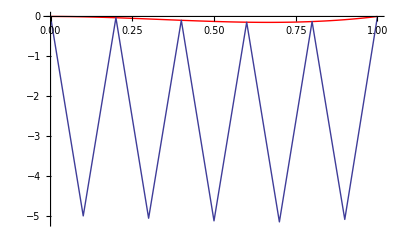

```mathematica
DF[10,a,b,c,f,x]
```